```mathematica
g=-Graphics-;
```

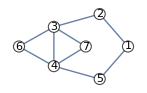

```mathematica
%1
```

```mathematica
FindClique[g]
```

{{3,4,6}}

```mathematica
GraphPlot@{1->2,1->5,2->3,3->4,4->5,3->6,4->6,6->3,6->4,4->3}
```

-Graphics-

```mathematica
Graph@{1->2,1->5,2->3,3->4,4->5,3->6,4->6,6->3,6->4,4->3}
```

-Graphics-

```mathematica
dji=EntityList[EntityClass["Financial","DowJonesIndustrialAverageComponents"]]
```

{3M,American Express,Apple,Boeing,Caterpillar,Chevron,Cisco,Coca-Cola,Disney,DowDuPont Inc,Exxon Mobil,Goldman Sachs,Home Depot,Intel,IBM,Johnson & Johnson,JPMorgan Chase,McDonald's,Merck & Co.,Microsoft,Nike,Pfizer,Procter & Gamble,Travelers,UnitedHealth,United Technologies,Verizon Communications,Visa,Walgreens Boots Alliance Inc,Wal-Mart Stores}

```mathematica
r=FinancialData[#,"Return",{{2012,1,1},{2012,5,25}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],{},TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{{10}}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{3M,American Express,Apple,Boeing,Caterpillar,Chevron,Cisco,Coca-Cola,Disney,Exxon Mobil,Goldman Sachs,Home Depot,Intel,IBM,Johnson & Johnson,JPMorgan Chase,McDonald's,Merck & Co.,Microsoft,Nike,Pfizer,Procter & Gamble,Travelers,UnitedHealth,United Technologies,Verizon Communications,Visa,Walgreens Boots Alliance Inc,Wal-Mart Stores}

{{1.,0.535052,0.266607,0.63917,0.701078,0.506136,0.317091,0.48702,0.546488,0.610451,0.555847,0.51327,0.419862,0.478354,0.535456,0.465976,0.230529,0.441294,0.397125,0.350554,0.418175,0.241169,0.425279,0.241406,0.690937,0.317349,0.30304,0.337252,0.120268},{0.535052,1.,0.445697,0.600729,0.425255,0.378291,0.257709,0.326095,0.47181,0.368978,0.460853,0.496262,0.372889,0.314697,0.397281,0.454557,0.395833,0.203622,0.326278,0.349236,0.340586,0.106759,0.439587,0.219772,0.506479,0.219996,0.412413,0.247793,0.0557047},{0.266607,0.445697,1.,0.588599,0.195374,0.296163,0.199525,0.319381,0.346083,0.179483,0.113306,0.336631,0.207235,0.254134,0.192144,0.20252,0.337086,0.0396893,0.175379,0.309589,0.193348,0.100186,0.0938483,0.296793,0.331367,-0.0751552,0.293361,0.265702,-0.00398789},{0.63917,0.600729,0.588599,1.,0.476245,0.45475,0.318563,0.470862,0.488705,0.484771,0.359001,0.516823,0.42304,0.463508,0.451429,0.292143,0.374176,0.243956,0.392573,0.421667,0.362508,0.136489,0.420186,0.31239,0.615824,0.196035,0.485701,0.305578,0.0387108},{0.701078,0.425255,0.195374,0.476245,1.,0.411664,0.269344,0.254443,0.461766,0.481615,0.486922,0.462135,0.37087,0.23628,0.25745,0.382594,0.262221,0.228292,0.356168,0.289871,0.278148,0.0321322,0.324321,0.215139,0.643949,0.175868,0.293338,0.223794,0.0423322},{0.506136,0.378291,0.296163,0.45475,0.411664,1.,0.172394,0.484465,0.492295,0.687175,0.313227,0.367459,0.370372,0.422559,0.484212,0.301134,0.243644,0.275595,0.358796,0.117637,0.379638,0.210015,0.351,0.261035,0.424986,0.350562,0.196466,0.293006,0.150102},{0.317091,0.257709,0.199525,0.318563,0.269344,0.172394,1.,0.0959376,0.271436,0.272691,0.324511,0.176494,0.253292,0.274602,0.147868,0.29476,0.230721,0.170096,0.260565,0.311937,0.0588055,-0.0429606,0.0959999,0.0765487,0.230037,0.0239319,0.0506904,0.129215,0.12337},{0.48702,0.326095,0.319381,0.470862,0.254443,0.484465,0.0959376,1.,0.448519,0.461163,0.136362,0.420693,0.295991,0.427817,0.450122,0.234726,0.280727,0.279846,0.278438,0.2569,0.382064,0.22799,0.379909,0.265347,0.388042,0.206407,0.161048,0.336957,0.141801},{0.546488,0.47181,0.346083,0.488705,0.461766,0.492295,0.271436,0.448519,1.,0.559878,0.447959,0.436663,0.446528,0.370477,0.353107,0.427573,0.232832,0.385482,0.455026,0.348829,0.430879,0.232301,0.36287,0.229427,0.488287,0.2835,0.274306,0.297618,0.197786},{0.610451,0.368978,0.179483,0.484771,0.481615,0.687175,0.272691,0.461163,0.559878,1.,0.427184,0.443986,0.401084,0.395913,0.427532,0.304327,0.366501,0.457123,0.411736,0.222109,0.445195,0.211761,0.341907,0.151159,0.389034,0.342026,0.142194,0.315047,0.0653726},{0.555847,0.460853,0.113306,0.359001,0.486922,0.313227,0.324511,0.136362,0.447959,0.427184,1.,0.355454,0.442704,0.350417,0.371433,0.740691,0.156502,0.197244,0.260099,0.199281,0.257097,0.0310844,0.334164,0.0357119,0.512603,0.256273,0.22557,0.2013,0.110314},{0.51327,0.496262,0.336631,0.516823,0.462135,0.367459,0.176494,0.420693,0.436663,0.443986,0.355454,1.,0.40772,0.222333,0.330387,0.410373,0.365684,0.349059,0.210254,0.432541,0.186963,0.171052,0.240475,0.13217,0.441717,0.0955981,0.280489,0.219521,0.044059},{0.419862,0.372889,0.207235,0.42304,0.37087,0.370372,0.253292,0.295991,0.446528,0.401084,0.442704,0.40772,1.,0.53653,0.318901,0.405955,0.300486,0.196208,0.518076,0.430589,0.175608,0.0303429,0.265616,0.188151,0.466755,0.186334,0.14531,0.166536,0.188974},{0.478354,0.314697,0.254134,0.463508,0.23628,0.422559,0.274602,0.427817,0.370477,0.395913,0.350417,0.222333,0.53653,1.,0.52043,0.347534,0.23379,0.306139,0.51319,0.285144,0.263204,0.120045,0.360389,0.214004,0.38782,0.231705,0.203956,0.212934,0.154828},{0.535456,0.397281,0.192144,0.451429,0.25745,0.484212,0.147868,0.450122,0.353107,0.427532,0.371433,0.330387,0.318901,0.52043,1.,0.336526,0.241921,0.496051,0.366132,0.223974,0.390937,0.315945,0.393817,0.183841,0.369277,0.344008,0.19846,0.144471,0.179371},{0.465976,0.454557,0.20252,0.292143,0.382594,0.301134,0.29476,0.234726,0.427573,0.304327,0.740691,0.410373,0.405955,0.347534,0.336526,1.,0.215763,0.242247,0.225846,0.2215,0.243294,0.073625,0.349113,0.109767,0.461147,0.150272,0.126592,0.273989,0.0326597},{0.230529,0.395833,0.337086,0.374176,0.262221,0.243644,0.230721,0.280727,0.232832,0.366501,0.156502,0.365684,0.300486,0.23379,0.241921,0.215763,1.,0.2073,0.322115,0.431793,0.1716,-0.00966629,0.205383,0.105429,0.276882,0.0695235,0.143913,0.128899,0.00845955},{0.441294,0.203622,0.0396893,0.243956,0.228292,0.275595,0.170096,0.279846,0.385482,0.457123,0.197244,0.349059,0.196208,0.306139,0.496051,0.242247,0.2073,1.,0.199176,0.232096,0.385882,0.299061,0.37921,0.0303744,0.299065,0.24276,0.114084,0.245029,0.230796},{0.397125,0.326278,0.175379,0.392573,0.356168,0.358796,0.260565,0.278438,0.455026,0.411736,0.260099,0.210254,0.518076,0.51319,0.366132,0.225846,0.322115,0.199176,1.,0.284379,0.343711,0.205954,0.398853,0.287317,0.386342,0.214354,0.0823382,0.108215,0.176447},{0.350554,0.349236,0.309589,0.421667,0.289871,0.117637,0.311937,0.2569,0.348829,0.222109,0.199281,0.432541,0.430589,0.285144,0.223974,0.2215,0.431793,0.232096,0.284379,1.,0.138365,0.110249,0.210696,0.152177,0.389147,0.133214,0.203705,0.0940769,0.190837},{0.418175,0.340586,0.193348,0.362508,0.278148,0.379638,0.0588055,0.382064,0.430879,0.445195,0.257097,0.186963,0.175608,0.263204,0.390937,0.243294,0.1716,0.385882,0.343711,0.138365,1.,0.144261,0.312022,0.235356,0.39753,0.258176,0.149028,0.281391,0.154388},{0.241169,0.106759,0.100186,0.136489,0.0321322,0.210015,-0.0429606,0.22799,0.232301,0.211761,0.0310844,0.171052,0.0303429,0.120045,0.315945,0.073625,-0.00966629,0.299061,0.205954,0.110249,0.144261,1.,0.253272,0.119433,0.0616163,0.154601,0.0696068,0.152004,0.12831},{0.425279,0.439587,0.0938483,0.420186,0.324321,0.351,0.0959999,0.379909,0.36287,0.341907,0.334164,0.240475,0.265616,0.360389,0.393817,0.349113,0.205383,0.37921,0.398853,0.210696,0.312022,0.253272,1.,0.290058,0.304597,0.438375,0.105523,0.199665,0.153917},{0.241406,0.219772,0.296793,0.31239,0.215139,0.261035,0.0765487,0.265347,0.229427,0.151159,0.0357119,0.13217,0.188151,0.214004,0.183841,0.109767,0.105429,0.0303744,0.287317,0.152177,0.235356,0.119433,0.290058,1.,0.400304,0.0986594,0.288204,0.121546,0.0388047},{0.690937,0.506479,0.331367,0.615824,0.643949,0.424986,0.230037,0.388042,0.488287,0.389034,0.512603,0.441717,0.466755,0.38782,0.369277,0.461147,0.276882,0.299065,0.386342,0.389147,0.39753,0.0616163,0.304597,0.400304,1.,0.339653,0.399623,0.370982,0.244101},{0.317349,0.219996,-0.0751552,0.196035,0.175868,0.350562,0.0239319,0.206407,0.2835,0.342026,0.256273,0.0955981,0.186334,0.231705,0.344008,0.150272,0.0695235,0.24276,0.214354,0.133214,0.258176,0.154601,0.438375,0.0986594,0.339653,1.,0.0225456,0.116558,0.260345},{0.30304,0.412413,0.293361,0.485701,0.293338,0.196466,0.0506904,0.161048,0.274306,0.142194,0.22557,0.280489,0.14531,0.203956,0.19846,0.126592,0.143913,0.114084,0.0823382,0.203705,0.149028,0.0696068,0.105523,0.288204,0.399623,0.0225456,1.,0.275029,0.100794},{0.337252,0.247793,0.265702,0.305578,0.223794,0.293006,0.129215,0.336957,0.297618,0.315047,0.2013,0.219521,0.166536,0.212934,0.144471,0.273989,0.128899,0.245029,0.108215,0.0940769,0.281391,0.152004,0.199665,0.121546,0.370982,0.116558,0.275029,1.,0.190001},{0.120268,0.0557047,-0.00398789,0.0387108,0.0423322,0.150102,0.12337,0.141801,0.197786,0.0653726,0.110314,0.044059,0.188974,0.154828,0.179371,0.0326597,0.00845955,0.230796,0.176447,0.190837,0.154388,0.12831,0.153917,0.0388047,0.244101,0.260345,0.100794,0.190001,1.}}

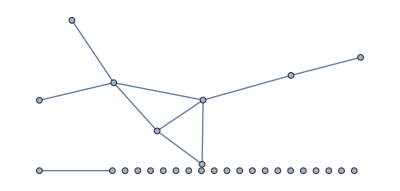

```mathematica
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58]]
```

```mathematica
stocks=First[FindClique[g]]
```

{3M,Boeing,United Technologies}

```mathematica
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

General::stop: Further output of FinancialData::dlfail will be suppressed during this calculation.

DateListPlot::dtvals: Unable to automatically determine horizontal coordinates for the given data and DataRange.

DateListPlot::ldata: {$Failed,$Failed,$Failed} is not a valid dataset or list of datasets.

DateListPlot[{$Failed,$Failed,$Failed},Joined→True,AspectRatio→1/5]

```mathematica
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

General::stop: Further output of FinancialData::dlfail will be suppressed during this calculation.

DateListPlot::dtvals: Unable to automatically determine horizontal coordinates for the given data and DataRange.

DateListPlot::ldata: {$Failed,$Failed,$Failed} is not a valid dataset or list of datasets.

DateListPlot[{$Failed,$Failed,$Failed},Joined→True,AspectRatio→1/5]

```mathematica
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

DateListPlot::ldata: … is not a valid dataset or list of datasets.

DateListPlot[{$Failed,TimeSeries[…],TimeSeries[…]},Joined→True,AspectRatio→1/5]

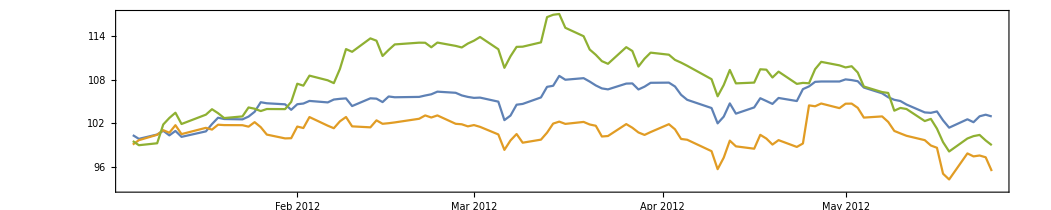

```mathematica
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5]
```

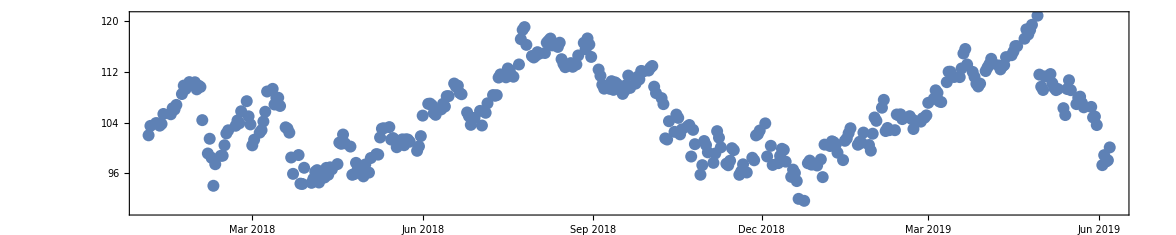

```mathematica
DateListPlot[
FinancialData["NASDAQ:GOOG", "CumulativeReturn", {{2018},{2019}}],
Joined->False, AspectRatio->1/5]
```

```mathematica
Variance[{4}]
```

Variance::shlen: The argument {4} should have at least two elements.

Variance[{4}]

```mathematica
Variance[{4,4}]
```

0

{3M,American Express,Apple,Boeing,Caterpillar,Chevron,Cisco,Coca-Cola,Disney,DowDuPont Inc,Exxon Mobil,Goldman Sachs,Home Depot,Intel,IBM,Johnson & Johnson,JPMorgan Chase,McDonald's,Merck & Co.,Microsoft,Nike,Pfizer,Procter & Gamble,Travelers,UnitedHealth,United Technologies,Verizon Communications,Visa,Walgreens Boots Alliance Inc,Wal-Mart Stores}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],{},TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{{10}}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{3M,American Express,Apple,Boeing,Caterpillar,Chevron,Cisco,Coca-Cola,Disney,Exxon Mobil,Goldman Sachs,Home Depot,Intel,IBM,Johnson & Johnson,JPMorgan Chase,McDonald's,Merck & Co.,Microsoft,Nike,Pfizer,Procter & Gamble,Travelers,UnitedHealth,United Technologies,Verizon Communications,Visa,Walgreens Boots Alliance Inc,Wal-Mart Stores}

{{1.,0.535052,0.266607,0.63917,0.701078,0.506136,0.317091,0.48702,0.546488,0.610451,0.555847,0.51327,0.419862,0.478354,0.535456,0.465976,0.230529,0.441294,0.397125,0.350554,0.418175,0.241169,0.425279,0.241406,0.690937,0.317349,0.30304,0.337252,0.120268},{0.535052,1.,0.445697,0.600729,0.425255,0.378291,0.257709,0.326095,0.47181,0.368978,0.460853,0.496262,0.372889,0.314697,0.397281,0.454557,0.395833,0.203622,0.326278,0.349236,0.340586,0.106759,0.439587,0.219772,0.506479,0.219996,0.412413,0.247793,0.0557047},{0.266607,0.445697,1.,0.588599,0.195374,0.296163,0.199525,0.319381,0.346083,0.179483,0.113306,0.336631,0.207235,0.254134,0.192144,0.20252,0.337086,0.0396893,0.175379,0.309589,0.193348,0.100186,0.0938483,0.296793,0.331367,-0.0751552,0.293361,0.265702,-0.00398789},{0.63917,0.600729,0.588599,1.,0.476245,0.45475,0.318563,0.470862,0.488705,0.484771,0.359001,0.516823,0.42304,0.463508,0.451429,0.292143,0.374176,0.243956,0.392573,0.421667,0.362508,0.136489,0.420186,0.31239,0.615824,0.196035,0.485701,0.305578,0.0387108},{0.701078,0.425255,0.195374,0.476245,1.,0.411664,0.269344,0.254443,0.461766,0.481615,0.486922,0.462135,0.37087,0.23628,0.25745,0.382594,0.262221,0.228292,0.356168,0.289871,0.278148,0.0321322,0.324321,0.215139,0.643949,0.175868,0.293338,0.223794,0.0423322},{0.506136,0.378291,0.296163,0.45475,0.411664,1.,0.172394,0.484465,0.492295,0.687175,0.313227,0.367459,0.370372,0.422559,0.484212,0.301134,0.243644,0.275595,0.358796,0.117637,0.379638,0.210015,0.351,0.261035,0.424986,0.350562,0.196466,0.293006,0.150102},{0.317091,0.257709,0.199525,0.318563,0.269344,0.172394,1.,0.0959376,0.271436,0.272691,0.324511,0.176494,0.253292,0.274602,0.147868,0.29476,0.230721,0.170096,0.260565,0.311937,0.0588055,-0.0429606,0.0959999,0.0765487,0.230037,0.0239319,0.0506904,0.129215,0.12337},{0.48702,0.326095,0.319381,0.470862,0.254443,0.484465,0.0959376,1.,0.448519,0.461163,0.136362,0.420693,0.295991,0.427817,0.450122,0.234726,0.280727,0.279846,0.278438,0.2569,0.382064,0.22799,0.379909,0.265347,0.388042,0.206407,0.161048,0.336957,0.141801},{0.546488,0.47181,0.346083,0.488705,0.461766,0.492295,0.271436,0.448519,1.,0.559878,0.447959,0.436663,0.446528,0.370477,0.353107,0.427573,0.232832,0.385482,0.455026,0.348829,0.430879,0.232301,0.36287,0.229427,0.488287,0.2835,0.274306,0.297618,0.197786},{0.610451,0.368978,0.179483,0.484771,0.481615,0.687175,0.272691,0.461163,0.559878,1.,0.427184,0.443986,0.401084,0.395913,0.427532,0.304327,0.366501,0.457123,0.411736,0.222109,0.445195,0.211761,0.341907,0.151159,0.389034,0.342026,0.142194,0.315047,0.0653726},{0.555847,0.460853,0.113306,0.359001,0.486922,0.313227,0.324511,0.136362,0.447959,0.427184,1.,0.355454,0.442704,0.350417,0.371433,0.740691,0.156502,0.197244,0.260099,0.199281,0.257097,0.0310844,0.334164,0.0357119,0.512603,0.256273,0.22557,0.2013,0.110314},{0.51327,0.496262,0.336631,0.516823,0.462135,0.367459,0.176494,0.420693,0.436663,0.443986,0.355454,1.,0.40772,0.222333,0.330387,0.410373,0.365684,0.349059,0.210254,0.432541,0.186963,0.171052,0.240475,0.13217,0.441717,0.0955981,0.280489,0.219521,0.044059},{0.419862,0.372889,0.207235,0.42304,0.37087,0.370372,0.253292,0.295991,0.446528,0.401084,0.442704,0.40772,1.,0.53653,0.318901,0.405955,0.300486,0.196208,0.518076,0.430589,0.175608,0.0303429,0.265616,0.188151,0.466755,0.186334,0.14531,0.166536,0.188974},{0.478354,0.314697,0.254134,0.463508,0.23628,0.422559,0.274602,0.427817,0.370477,0.395913,0.350417,0.222333,0.53653,1.,0.52043,0.347534,0.23379,0.306139,0.51319,0.285144,0.263204,0.120045,0.360389,0.214004,0.38782,0.231705,0.203956,0.212934,0.154828},{0.535456,0.397281,0.192144,0.451429,0.25745,0.484212,0.147868,0.450122,0.353107,0.427532,0.371433,0.330387,0.318901,0.52043,1.,0.336526,0.241921,0.496051,0.366132,0.223974,0.390937,0.315945,0.393817,0.183841,0.369277,0.344008,0.19846,0.144471,0.179371},{0.465976,0.454557,0.20252,0.292143,0.382594,0.301134,0.29476,0.234726,0.427573,0.304327,0.740691,0.410373,0.405955,0.347534,0.336526,1.,0.215763,0.242247,0.225846,0.2215,0.243294,0.073625,0.349113,0.109767,0.461147,0.150272,0.126592,0.273989,0.0326597},{0.230529,0.395833,0.337086,0.374176,0.262221,0.243644,0.230721,0.280727,0.232832,0.366501,0.156502,0.365684,0.300486,0.23379,0.241921,0.215763,1.,0.2073,0.322115,0.431793,0.1716,-0.00966629,0.205383,0.105429,0.276882,0.0695235,0.143913,0.128899,0.00845955},{0.441294,0.203622,0.0396893,0.243956,0.228292,0.275595,0.170096,0.279846,0.385482,0.457123,0.197244,0.349059,0.196208,0.306139,0.496051,0.242247,0.2073,1.,0.199176,0.232096,0.385882,0.299061,0.37921,0.0303744,0.299065,0.24276,0.114084,0.245029,0.230796},{0.397125,0.326278,0.175379,0.392573,0.356168,0.358796,0.260565,0.278438,0.455026,0.411736,0.260099,0.210254,0.518076,0.51319,0.366132,0.225846,0.322115,0.199176,1.,0.284379,0.343711,0.205954,0.398853,0.287317,0.386342,0.214354,0.0823382,0.108215,0.176447},{0.350554,0.349236,0.309589,0.421667,0.289871,0.117637,0.311937,0.2569,0.348829,0.222109,0.199281,0.432541,0.430589,0.285144,0.223974,0.2215,0.431793,0.232096,0.284379,1.,0.138365,0.110249,0.210696,0.152177,0.389147,0.133214,0.203705,0.0940769,0.190837},{0.418175,0.340586,0.193348,0.362508,0.278148,0.379638,0.0588055,0.382064,0.430879,0.445195,0.257097,0.186963,0.175608,0.263204,0.390937,0.243294,0.1716,0.385882,0.343711,0.138365,1.,0.144261,0.312022,0.235356,0.39753,0.258176,0.149028,0.281391,0.154388},{0.241169,0.106759,0.100186,0.136489,0.0321322,0.210015,-0.0429606,0.22799,0.232301,0.211761,0.0310844,0.171052,0.0303429,0.120045,0.315945,0.073625,-0.00966629,0.299061,0.205954,0.110249,0.144261,1.,0.253272,0.119433,0.0616163,0.154601,0.0696068,0.152004,0.12831},{0.425279,0.439587,0.0938483,0.420186,0.324321,0.351,0.0959999,0.379909,0.36287,0.341907,0.334164,0.240475,0.265616,0.360389,0.393817,0.349113,0.205383,0.37921,0.398853,0.210696,0.312022,0.253272,1.,0.290058,0.304597,0.438375,0.105523,0.199665,0.153917},{0.241406,0.219772,0.296793,0.31239,0.215139,0.261035,0.0765487,0.265347,0.229427,0.151159,0.0357119,0.13217,0.188151,0.214004,0.183841,0.109767,0.105429,0.0303744,0.287317,0.152177,0.235356,0.119433,0.290058,1.,0.400304,0.0986594,0.288204,0.121546,0.0388047},{0.690937,0.506479,0.331367,0.615824,0.643949,0.424986,0.230037,0.388042,0.488287,0.389034,0.512603,0.441717,0.466755,0.38782,0.369277,0.461147,0.276882,0.299065,0.386342,0.389147,0.39753,0.0616163,0.304597,0.400304,1.,0.339653,0.399623,0.370982,0.244101},{0.317349,0.219996,-0.0751552,0.196035,0.175868,0.350562,0.0239319,0.206407,0.2835,0.342026,0.256273,0.0955981,0.186334,0.231705,0.344008,0.150272,0.0695235,0.24276,0.214354,0.133214,0.258176,0.154601,0.438375,0.0986594,0.339653,1.,0.0225456,0.116558,0.260345},{0.30304,0.412413,0.293361,0.485701,0.293338,0.196466,0.0506904,0.161048,0.274306,0.142194,0.22557,0.280489,0.14531,0.203956,0.19846,0.126592,0.143913,0.114084,0.0823382,0.203705,0.149028,0.0696068,0.105523,0.288204,0.399623,0.0225456,1.,0.275029,0.100794},{0.337252,0.247793,0.265702,0.305578,0.223794,0.293006,0.129215,0.336957,0.297618,0.315047,0.2013,0.219521,0.166536,0.212934,0.144471,0.273989,0.128899,0.245029,0.108215,0.0940769,0.281391,0.152004,0.199665,0.121546,0.370982,0.116558,0.275029,1.,0.190001},{0.120268,0.0557047,-0.00398789,0.0387108,0.0423322,0.150102,0.12337,0.141801,0.197786,0.0653726,0.110314,0.044059,0.188974,0.154828,0.179371,0.0326597,0.00845955,0.230796,0.176447,0.190837,0.154388,0.12831,0.153917,0.0388047,0.244101,0.260345,0.100794,0.190001,1.}}

-Graphics-

{3M,Boeing,United Technologies}

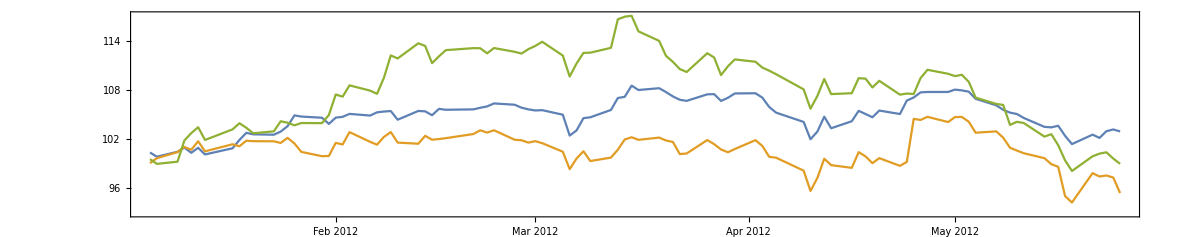

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji=EntityList[EntityClass["Financial","DowJonesIndustrialAverageComponents"]]
r=FinancialData[#,"Return",{{2012,1,1},{2012,5,25}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58]]
stocks=First[FindClique[g]]
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5]
```

{3M,American Express,Apple,Boeing,Caterpillar,Chevron,Cisco,Coca-Cola,Disney,DowDuPont Inc,Exxon Mobil,Goldman Sachs,Home Depot,Intel,IBM,Johnson & Johnson,JPMorgan Chase,McDonald's,Merck & Co.,Microsoft,Nike,Pfizer,Procter & Gamble,Travelers,UnitedHealth,United Technologies,Verizon Communications,Visa,Walgreens Boots Alliance Inc,Wal-Mart Stores}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],{},TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{{10}}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{3M,American Express,Apple,Boeing,Caterpillar,Chevron,Cisco,Coca-Cola,Disney,Exxon Mobil,Goldman Sachs,Home Depot,Intel,IBM,Johnson & Johnson,JPMorgan Chase,McDonald's,Merck & Co.,Microsoft,Nike,Pfizer,Procter & Gamble,Travelers,UnitedHealth,United Technologies,Verizon Communications,Visa,Walgreens Boots Alliance Inc,Wal-Mart Stores}

{{1.,0.535052,0.266607,0.63917,0.701078,0.506136,0.317091,0.48702,0.546488,0.610451,0.555847,0.51327,0.419862,0.478354,0.535456,0.465976,0.230529,0.441294,0.397125,0.350554,0.418175,0.241169,0.425279,0.241406,0.690937,0.317349,0.30304,0.337252,0.120268},{0.535052,1.,0.445697,0.600729,0.425255,0.378291,0.257709,0.326095,0.47181,0.368978,0.460853,0.496262,0.372889,0.314697,0.397281,0.454557,0.395833,0.203622,0.326278,0.349236,0.340586,0.106759,0.439587,0.219772,0.506479,0.219996,0.412413,0.247793,0.0557047},{0.266607,0.445697,1.,0.588599,0.195374,0.296163,0.199525,0.319381,0.346083,0.179483,0.113306,0.336631,0.207235,0.254134,0.192144,0.20252,0.337086,0.0396893,0.175379,0.309589,0.193348,0.100186,0.0938483,0.296793,0.331367,-0.0751552,0.293361,0.265702,-0.00398789},{0.63917,0.600729,0.588599,1.,0.476245,0.45475,0.318563,0.470862,0.488705,0.484771,0.359001,0.516823,0.42304,0.463508,0.451429,0.292143,0.374176,0.243956,0.392573,0.421667,0.362508,0.136489,0.420186,0.31239,0.615824,0.196035,0.485701,0.305578,0.0387108},{0.701078,0.425255,0.195374,0.476245,1.,0.411664,0.269344,0.254443,0.461766,0.481615,0.486922,0.462135,0.37087,0.23628,0.25745,0.382594,0.262221,0.228292,0.356168,0.289871,0.278148,0.0321322,0.324321,0.215139,0.643949,0.175868,0.293338,0.223794,0.0423322},{0.506136,0.378291,0.296163,0.45475,0.411664,1.,0.172394,0.484465,0.492295,0.687175,0.313227,0.367459,0.370372,0.422559,0.484212,0.301134,0.243644,0.275595,0.358796,0.117637,0.379638,0.210015,0.351,0.261035,0.424986,0.350562,0.196466,0.293006,0.150102},{0.317091,0.257709,0.199525,0.318563,0.269344,0.172394,1.,0.0959376,0.271436,0.272691,0.324511,0.176494,0.253292,0.274602,0.147868,0.29476,0.230721,0.170096,0.260565,0.311937,0.0588055,-0.0429606,0.0959999,0.0765487,0.230037,0.0239319,0.0506904,0.129215,0.12337},{0.48702,0.326095,0.319381,0.470862,0.254443,0.484465,0.0959376,1.,0.448519,0.461163,0.136362,0.420693,0.295991,0.427817,0.450122,0.234726,0.280727,0.279846,0.278438,0.2569,0.382064,0.22799,0.379909,0.265347,0.388042,0.206407,0.161048,0.336957,0.141801},{0.546488,0.47181,0.346083,0.488705,0.461766,0.492295,0.271436,0.448519,1.,0.559878,0.447959,0.436663,0.446528,0.370477,0.353107,0.427573,0.232832,0.385482,0.455026,0.348829,0.430879,0.232301,0.36287,0.229427,0.488287,0.2835,0.274306,0.297618,0.197786},{0.610451,0.368978,0.179483,0.484771,0.481615,0.687175,0.272691,0.461163,0.559878,1.,0.427184,0.443986,0.401084,0.395913,0.427532,0.304327,0.366501,0.457123,0.411736,0.222109,0.445195,0.211761,0.341907,0.151159,0.389034,0.342026,0.142194,0.315047,0.0653726},{0.555847,0.460853,0.113306,0.359001,0.486922,0.313227,0.324511,0.136362,0.447959,0.427184,1.,0.355454,0.442704,0.350417,0.371433,0.740691,0.156502,0.197244,0.260099,0.199281,0.257097,0.0310844,0.334164,0.0357119,0.512603,0.256273,0.22557,0.2013,0.110314},{0.51327,0.496262,0.336631,0.516823,0.462135,0.367459,0.176494,0.420693,0.436663,0.443986,0.355454,1.,0.40772,0.222333,0.330387,0.410373,0.365684,0.349059,0.210254,0.432541,0.186963,0.171052,0.240475,0.13217,0.441717,0.0955981,0.280489,0.219521,0.044059},{0.419862,0.372889,0.207235,0.42304,0.37087,0.370372,0.253292,0.295991,0.446528,0.401084,0.442704,0.40772,1.,0.53653,0.318901,0.405955,0.300486,0.196208,0.518076,0.430589,0.175608,0.0303429,0.265616,0.188151,0.466755,0.186334,0.14531,0.166536,0.188974},{0.478354,0.314697,0.254134,0.463508,0.23628,0.422559,0.274602,0.427817,0.370477,0.395913,0.350417,0.222333,0.53653,1.,0.52043,0.347534,0.23379,0.306139,0.51319,0.285144,0.263204,0.120045,0.360389,0.214004,0.38782,0.231705,0.203956,0.212934,0.154828},{0.535456,0.397281,0.192144,0.451429,0.25745,0.484212,0.147868,0.450122,0.353107,0.427532,0.371433,0.330387,0.318901,0.52043,1.,0.336526,0.241921,0.496051,0.366132,0.223974,0.390937,0.315945,0.393817,0.183841,0.369277,0.344008,0.19846,0.144471,0.179371},{0.465976,0.454557,0.20252,0.292143,0.382594,0.301134,0.29476,0.234726,0.427573,0.304327,0.740691,0.410373,0.405955,0.347534,0.336526,1.,0.215763,0.242247,0.225846,0.2215,0.243294,0.073625,0.349113,0.109767,0.461147,0.150272,0.126592,0.273989,0.0326597},{0.230529,0.395833,0.337086,0.374176,0.262221,0.243644,0.230721,0.280727,0.232832,0.366501,0.156502,0.365684,0.300486,0.23379,0.241921,0.215763,1.,0.2073,0.322115,0.431793,0.1716,-0.00966629,0.205383,0.105429,0.276882,0.0695235,0.143913,0.128899,0.00845955},{0.441294,0.203622,0.0396893,0.243956,0.228292,0.275595,0.170096,0.279846,0.385482,0.457123,0.197244,0.349059,0.196208,0.306139,0.496051,0.242247,0.2073,1.,0.199176,0.232096,0.385882,0.299061,0.37921,0.0303744,0.299065,0.24276,0.114084,0.245029,0.230796},{0.397125,0.326278,0.175379,0.392573,0.356168,0.358796,0.260565,0.278438,0.455026,0.411736,0.260099,0.210254,0.518076,0.51319,0.366132,0.225846,0.322115,0.199176,1.,0.284379,0.343711,0.205954,0.398853,0.287317,0.386342,0.214354,0.0823382,0.108215,0.176447},{0.350554,0.349236,0.309589,0.421667,0.289871,0.117637,0.311937,0.2569,0.348829,0.222109,0.199281,0.432541,0.430589,0.285144,0.223974,0.2215,0.431793,0.232096,0.284379,1.,0.138365,0.110249,0.210696,0.152177,0.389147,0.133214,0.203705,0.0940769,0.190837},{0.418175,0.340586,0.193348,0.362508,0.278148,0.379638,0.0588055,0.382064,0.430879,0.445195,0.257097,0.186963,0.175608,0.263204,0.390937,0.243294,0.1716,0.385882,0.343711,0.138365,1.,0.144261,0.312022,0.235356,0.39753,0.258176,0.149028,0.281391,0.154388},{0.241169,0.106759,0.100186,0.136489,0.0321322,0.210015,-0.0429606,0.22799,0.232301,0.211761,0.0310844,0.171052,0.0303429,0.120045,0.315945,0.073625,-0.00966629,0.299061,0.205954,0.110249,0.144261,1.,0.253272,0.119433,0.0616163,0.154601,0.0696068,0.152004,0.12831},{0.425279,0.439587,0.0938483,0.420186,0.324321,0.351,0.0959999,0.379909,0.36287,0.341907,0.334164,0.240475,0.265616,0.360389,0.393817,0.349113,0.205383,0.37921,0.398853,0.210696,0.312022,0.253272,1.,0.290058,0.304597,0.438375,0.105523,0.199665,0.153917},{0.241406,0.219772,0.296793,0.31239,0.215139,0.261035,0.0765487,0.265347,0.229427,0.151159,0.0357119,0.13217,0.188151,0.214004,0.183841,0.109767,0.105429,0.0303744,0.287317,0.152177,0.235356,0.119433,0.290058,1.,0.400304,0.0986594,0.288204,0.121546,0.0388047},{0.690937,0.506479,0.331367,0.615824,0.643949,0.424986,0.230037,0.388042,0.488287,0.389034,0.512603,0.441717,0.466755,0.38782,0.369277,0.461147,0.276882,0.299065,0.386342,0.389147,0.39753,0.0616163,0.304597,0.400304,1.,0.339653,0.399623,0.370982,0.244101},{0.317349,0.219996,-0.0751552,0.196035,0.175868,0.350562,0.0239319,0.206407,0.2835,0.342026,0.256273,0.0955981,0.186334,0.231705,0.344008,0.150272,0.0695235,0.24276,0.214354,0.133214,0.258176,0.154601,0.438375,0.0986594,0.339653,1.,0.0225456,0.116558,0.260345},{0.30304,0.412413,0.293361,0.485701,0.293338,0.196466,0.0506904,0.161048,0.274306,0.142194,0.22557,0.280489,0.14531,0.203956,0.19846,0.126592,0.143913,0.114084,0.0823382,0.203705,0.149028,0.0696068,0.105523,0.288204,0.399623,0.0225456,1.,0.275029,0.100794},{0.337252,0.247793,0.265702,0.305578,0.223794,0.293006,0.129215,0.336957,0.297618,0.315047,0.2013,0.219521,0.166536,0.212934,0.144471,0.273989,0.128899,0.245029,0.108215,0.0940769,0.281391,0.152004,0.199665,0.121546,0.370982,0.116558,0.275029,1.,0.190001},{0.120268,0.0557047,-0.00398789,0.0387108,0.0423322,0.150102,0.12337,0.141801,0.197786,0.0653726,0.110314,0.044059,0.188974,0.154828,0.179371,0.0326597,0.00845955,0.230796,0.176447,0.190837,0.154388,0.12831,0.153917,0.0388047,0.244101,0.260345,0.100794,0.190001,1.}}

-Graphics-

{3M,Boeing,United Technologies}

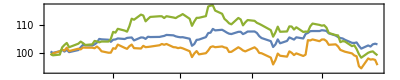

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji=EntityList[EntityClass["Financial","DowJonesIndustrialAverageComponents"]]
r=FinancialData[#,"Return",{{2012,1,1},{2012,5,25}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58]]
stocks=First[FindClique[g]]
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5, ImageSize->Full]
```

{3M,American Express,Apple,Boeing,Caterpillar,Chevron,Cisco,Coca-Cola,Disney,DowDuPont Inc,Exxon Mobil,Goldman Sachs,Home Depot,Intel,IBM,Johnson & Johnson,JPMorgan Chase,McDonald's,Merck & Co.,Microsoft,Nike,Pfizer,Procter & Gamble,Travelers,UnitedHealth,United Technologies,Verizon Communications,Visa,Walgreens Boots Alliance Inc,Wal-Mart Stores}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],{},TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{{10}}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{3M,American Express,Apple,Boeing,Caterpillar,Chevron,Cisco,Coca-Cola,Disney,Exxon Mobil,Goldman Sachs,Home Depot,Intel,IBM,Johnson & Johnson,JPMorgan Chase,McDonald's,Merck & Co.,Microsoft,Nike,Pfizer,Procter & Gamble,Travelers,UnitedHealth,United Technologies,Verizon Communications,Visa,Walgreens Boots Alliance Inc,Wal-Mart Stores}

{{1.,0.535052,0.266607,0.63917,0.701078,0.506136,0.317091,0.48702,0.546488,0.610451,0.555847,0.51327,0.419862,0.478354,0.535456,0.465976,0.230529,0.441294,0.397125,0.350554,0.418175,0.241169,0.425279,0.241406,0.690937,0.317349,0.30304,0.337252,0.120268},{0.535052,1.,0.445697,0.600729,0.425255,0.378291,0.257709,0.326095,0.47181,0.368978,0.460853,0.496262,0.372889,0.314697,0.397281,0.454557,0.395833,0.203622,0.326278,0.349236,0.340586,0.106759,0.439587,0.219772,0.506479,0.219996,0.412413,0.247793,0.0557047},{0.266607,0.445697,1.,0.588599,0.195374,0.296163,0.199525,0.319381,0.346083,0.179483,0.113306,0.336631,0.207235,0.254134,0.192144,0.20252,0.337086,0.0396893,0.175379,0.309589,0.193348,0.100186,0.0938483,0.296793,0.331367,-0.0751552,0.293361,0.265702,-0.00398789},{0.63917,0.600729,0.588599,1.,0.476245,0.45475,0.318563,0.470862,0.488705,0.484771,0.359001,0.516823,0.42304,0.463508,0.451429,0.292143,0.374176,0.243956,0.392573,0.421667,0.362508,0.136489,0.420186,0.31239,0.615824,0.196035,0.485701,0.305578,0.0387108},{0.701078,0.425255,0.195374,0.476245,1.,0.411664,0.269344,0.254443,0.461766,0.481615,0.486922,0.462135,0.37087,0.23628,0.25745,0.382594,0.262221,0.228292,0.356168,0.289871,0.278148,0.0321322,0.324321,0.215139,0.643949,0.175868,0.293338,0.223794,0.0423322},{0.506136,0.378291,0.296163,0.45475,0.411664,1.,0.172394,0.484465,0.492295,0.687175,0.313227,0.367459,0.370372,0.422559,0.484212,0.301134,0.243644,0.275595,0.358796,0.117637,0.379638,0.210015,0.351,0.261035,0.424986,0.350562,0.196466,0.293006,0.150102},{0.317091,0.257709,0.199525,0.318563,0.269344,0.172394,1.,0.0959376,0.271436,0.272691,0.324511,0.176494,0.253292,0.274602,0.147868,0.29476,0.230721,0.170096,0.260565,0.311937,0.0588055,-0.0429606,0.0959999,0.0765487,0.230037,0.0239319,0.0506904,0.129215,0.12337},{0.48702,0.326095,0.319381,0.470862,0.254443,0.484465,0.0959376,1.,0.448519,0.461163,0.136362,0.420693,0.295991,0.427817,0.450122,0.234726,0.280727,0.279846,0.278438,0.2569,0.382064,0.22799,0.379909,0.265347,0.388042,0.206407,0.161048,0.336957,0.141801},{0.546488,0.47181,0.346083,0.488705,0.461766,0.492295,0.271436,0.448519,1.,0.559878,0.447959,0.436663,0.446528,0.370477,0.353107,0.427573,0.232832,0.385482,0.455026,0.348829,0.430879,0.232301,0.36287,0.229427,0.488287,0.2835,0.274306,0.297618,0.197786},{0.610451,0.368978,0.179483,0.484771,0.481615,0.687175,0.272691,0.461163,0.559878,1.,0.427184,0.443986,0.401084,0.395913,0.427532,0.304327,0.366501,0.457123,0.411736,0.222109,0.445195,0.211761,0.341907,0.151159,0.389034,0.342026,0.142194,0.315047,0.0653726},{0.555847,0.460853,0.113306,0.359001,0.486922,0.313227,0.324511,0.136362,0.447959,0.427184,1.,0.355454,0.442704,0.350417,0.371433,0.740691,0.156502,0.197244,0.260099,0.199281,0.257097,0.0310844,0.334164,0.0357119,0.512603,0.256273,0.22557,0.2013,0.110314},{0.51327,0.496262,0.336631,0.516823,0.462135,0.367459,0.176494,0.420693,0.436663,0.443986,0.355454,1.,0.40772,0.222333,0.330387,0.410373,0.365684,0.349059,0.210254,0.432541,0.186963,0.171052,0.240475,0.13217,0.441717,0.0955981,0.280489,0.219521,0.044059},{0.419862,0.372889,0.207235,0.42304,0.37087,0.370372,0.253292,0.295991,0.446528,0.401084,0.442704,0.40772,1.,0.53653,0.318901,0.405955,0.300486,0.196208,0.518076,0.430589,0.175608,0.0303429,0.265616,0.188151,0.466755,0.186334,0.14531,0.166536,0.188974},{0.478354,0.314697,0.254134,0.463508,0.23628,0.422559,0.274602,0.427817,0.370477,0.395913,0.350417,0.222333,0.53653,1.,0.52043,0.347534,0.23379,0.306139,0.51319,0.285144,0.263204,0.120045,0.360389,0.214004,0.38782,0.231705,0.203956,0.212934,0.154828},{0.535456,0.397281,0.192144,0.451429,0.25745,0.484212,0.147868,0.450122,0.353107,0.427532,0.371433,0.330387,0.318901,0.52043,1.,0.336526,0.241921,0.496051,0.366132,0.223974,0.390937,0.315945,0.393817,0.183841,0.369277,0.344008,0.19846,0.144471,0.179371},{0.465976,0.454557,0.20252,0.292143,0.382594,0.301134,0.29476,0.234726,0.427573,0.304327,0.740691,0.410373,0.405955,0.347534,0.336526,1.,0.215763,0.242247,0.225846,0.2215,0.243294,0.073625,0.349113,0.109767,0.461147,0.150272,0.126592,0.273989,0.0326597},{0.230529,0.395833,0.337086,0.374176,0.262221,0.243644,0.230721,0.280727,0.232832,0.366501,0.156502,0.365684,0.300486,0.23379,0.241921,0.215763,1.,0.2073,0.322115,0.431793,0.1716,-0.00966629,0.205383,0.105429,0.276882,0.0695235,0.143913,0.128899,0.00845955},{0.441294,0.203622,0.0396893,0.243956,0.228292,0.275595,0.170096,0.279846,0.385482,0.457123,0.197244,0.349059,0.196208,0.306139,0.496051,0.242247,0.2073,1.,0.199176,0.232096,0.385882,0.299061,0.37921,0.0303744,0.299065,0.24276,0.114084,0.245029,0.230796},{0.397125,0.326278,0.175379,0.392573,0.356168,0.358796,0.260565,0.278438,0.455026,0.411736,0.260099,0.210254,0.518076,0.51319,0.366132,0.225846,0.322115,0.199176,1.,0.284379,0.343711,0.205954,0.398853,0.287317,0.386342,0.214354,0.0823382,0.108215,0.176447},{0.350554,0.349236,0.309589,0.421667,0.289871,0.117637,0.311937,0.2569,0.348829,0.222109,0.199281,0.432541,0.430589,0.285144,0.223974,0.2215,0.431793,0.232096,0.284379,1.,0.138365,0.110249,0.210696,0.152177,0.389147,0.133214,0.203705,0.0940769,0.190837},{0.418175,0.340586,0.193348,0.362508,0.278148,0.379638,0.0588055,0.382064,0.430879,0.445195,0.257097,0.186963,0.175608,0.263204,0.390937,0.243294,0.1716,0.385882,0.343711,0.138365,1.,0.144261,0.312022,0.235356,0.39753,0.258176,0.149028,0.281391,0.154388},{0.241169,0.106759,0.100186,0.136489,0.0321322,0.210015,-0.0429606,0.22799,0.232301,0.211761,0.0310844,0.171052,0.0303429,0.120045,0.315945,0.073625,-0.00966629,0.299061,0.205954,0.110249,0.144261,1.,0.253272,0.119433,0.0616163,0.154601,0.0696068,0.152004,0.12831},{0.425279,0.439587,0.0938483,0.420186,0.324321,0.351,0.0959999,0.379909,0.36287,0.341907,0.334164,0.240475,0.265616,0.360389,0.393817,0.349113,0.205383,0.37921,0.398853,0.210696,0.312022,0.253272,1.,0.290058,0.304597,0.438375,0.105523,0.199665,0.153917},{0.241406,0.219772,0.296793,0.31239,0.215139,0.261035,0.0765487,0.265347,0.229427,0.151159,0.0357119,0.13217,0.188151,0.214004,0.183841,0.109767,0.105429,0.0303744,0.287317,0.152177,0.235356,0.119433,0.290058,1.,0.400304,0.0986594,0.288204,0.121546,0.0388047},{0.690937,0.506479,0.331367,0.615824,0.643949,0.424986,0.230037,0.388042,0.488287,0.389034,0.512603,0.441717,0.466755,0.38782,0.369277,0.461147,0.276882,0.299065,0.386342,0.389147,0.39753,0.0616163,0.304597,0.400304,1.,0.339653,0.399623,0.370982,0.244101},{0.317349,0.219996,-0.0751552,0.196035,0.175868,0.350562,0.0239319,0.206407,0.2835,0.342026,0.256273,0.0955981,0.186334,0.231705,0.344008,0.150272,0.0695235,0.24276,0.214354,0.133214,0.258176,0.154601,0.438375,0.0986594,0.339653,1.,0.0225456,0.116558,0.260345},{0.30304,0.412413,0.293361,0.485701,0.293338,0.196466,0.0506904,0.161048,0.274306,0.142194,0.22557,0.280489,0.14531,0.203956,0.19846,0.126592,0.143913,0.114084,0.0823382,0.203705,0.149028,0.0696068,0.105523,0.288204,0.399623,0.0225456,1.,0.275029,0.100794},{0.337252,0.247793,0.265702,0.305578,0.223794,0.293006,0.129215,0.336957,0.297618,0.315047,0.2013,0.219521,0.166536,0.212934,0.144471,0.273989,0.128899,0.245029,0.108215,0.0940769,0.281391,0.152004,0.199665,0.121546,0.370982,0.116558,0.275029,1.,0.190001},{0.120268,0.0557047,-0.00398789,0.0387108,0.0423322,0.150102,0.12337,0.141801,0.197786,0.0653726,0.110314,0.044059,0.188974,0.154828,0.179371,0.0326597,0.00845955,0.230796,0.176447,0.190837,0.154388,0.12831,0.153917,0.0388047,0.244101,0.260345,0.100794,0.190001,1.}}

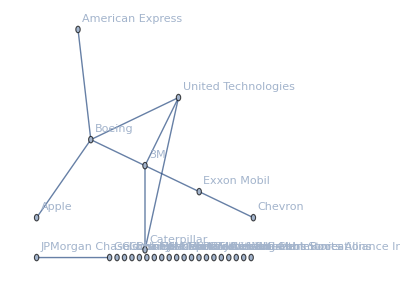

{3M,Boeing,United Technologies}

-Graphics-

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji=EntityList[EntityClass["Financial","DowJonesIndustrialAverageComponents"]]
r=FinancialData[#,"Return",{{2012,1,1},{2012,5,25}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58], GraphLayout->"RadialEmbedding", VertexLabels->"Name"]
stocks=First[FindClique[g]]
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5, ImageSize->Full]
```

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji=EntityList[EntityClass["Financial","DowJonesIndustrialAverageComponents"]]
r=FinancialData[#,"Return",{{2012,1,1},{2012,5,25}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58], GraphLayout->"RadialEmbedding", VertexLabels->"Name", ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5, ImageSize->Full]
```

{3M,American Express,Apple,Boeing,Caterpillar,Chevron,Cisco,Coca-Cola,Disney,DowDuPont Inc,Exxon Mobil,Goldman Sachs,Home Depot,Intel,IBM,Johnson & Johnson,JPMorgan Chase,McDonald's,Merck & Co.,Microsoft,Nike,Pfizer,Procter & Gamble,Travelers,UnitedHealth,United Technologies,Verizon Communications,Visa,Walgreens Boots Alliance Inc,Wal-Mart Stores}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],{},TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{{10}}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{3M,American Express,Apple,Boeing,Caterpillar,Chevron,Cisco,Coca-Cola,Disney,Exxon Mobil,Goldman Sachs,Home Depot,Intel,IBM,Johnson & Johnson,JPMorgan Chase,McDonald's,Merck & Co.,Microsoft,Nike,Pfizer,Procter & Gamble,Travelers,UnitedHealth,United Technologies,Verizon Communications,Visa,Walgreens Boots Alliance Inc,Wal-Mart Stores}

{{1.,0.535052,0.266607,0.63917,0.701078,0.506136,0.317091,0.48702,0.546488,0.610451,0.555847,0.51327,0.419862,0.478354,0.535456,0.465976,0.230529,0.441294,0.397125,0.350554,0.418175,0.241169,0.425279,0.241406,0.690937,0.317349,0.30304,0.337252,0.120268},{0.535052,1.,0.445697,0.600729,0.425255,0.378291,0.257709,0.326095,0.47181,0.368978,0.460853,0.496262,0.372889,0.314697,0.397281,0.454557,0.395833,0.203622,0.326278,0.349236,0.340586,0.106759,0.439587,0.219772,0.506479,0.219996,0.412413,0.247793,0.0557047},{0.266607,0.445697,1.,0.588599,0.195374,0.296163,0.199525,0.319381,0.346083,0.179483,0.113306,0.336631,0.207235,0.254134,0.192144,0.20252,0.337086,0.0396893,0.175379,0.309589,0.193348,0.100186,0.0938483,0.296793,0.331367,-0.0751552,0.293361,0.265702,-0.00398789},{0.63917,0.600729,0.588599,1.,0.476245,0.45475,0.318563,0.470862,0.488705,0.484771,0.359001,0.516823,0.42304,0.463508,0.451429,0.292143,0.374176,0.243956,0.392573,0.421667,0.362508,0.136489,0.420186,0.31239,0.615824,0.196035,0.485701,0.305578,0.0387108},{0.701078,0.425255,0.195374,0.476245,1.,0.411664,0.269344,0.254443,0.461766,0.481615,0.486922,0.462135,0.37087,0.23628,0.25745,0.382594,0.262221,0.228292,0.356168,0.289871,0.278148,0.0321322,0.324321,0.215139,0.643949,0.175868,0.293338,0.223794,0.0423322},{0.506136,0.378291,0.296163,0.45475,0.411664,1.,0.172394,0.484465,0.492295,0.687175,0.313227,0.367459,0.370372,0.422559,0.484212,0.301134,0.243644,0.275595,0.358796,0.117637,0.379638,0.210015,0.351,0.261035,0.424986,0.350562,0.196466,0.293006,0.150102},{0.317091,0.257709,0.199525,0.318563,0.269344,0.172394,1.,0.0959376,0.271436,0.272691,0.324511,0.176494,0.253292,0.274602,0.147868,0.29476,0.230721,0.170096,0.260565,0.311937,0.0588055,-0.0429606,0.0959999,0.0765487,0.230037,0.0239319,0.0506904,0.129215,0.12337},{0.48702,0.326095,0.319381,0.470862,0.254443,0.484465,0.0959376,1.,0.448519,0.461163,0.136362,0.420693,0.295991,0.427817,0.450122,0.234726,0.280727,0.279846,0.278438,0.2569,0.382064,0.22799,0.379909,0.265347,0.388042,0.206407,0.161048,0.336957,0.141801},{0.546488,0.47181,0.346083,0.488705,0.461766,0.492295,0.271436,0.448519,1.,0.559878,0.447959,0.436663,0.446528,0.370477,0.353107,0.427573,0.232832,0.385482,0.455026,0.348829,0.430879,0.232301,0.36287,0.229427,0.488287,0.2835,0.274306,0.297618,0.197786},{0.610451,0.368978,0.179483,0.484771,0.481615,0.687175,0.272691,0.461163,0.559878,1.,0.427184,0.443986,0.401084,0.395913,0.427532,0.304327,0.366501,0.457123,0.411736,0.222109,0.445195,0.211761,0.341907,0.151159,0.389034,0.342026,0.142194,0.315047,0.0653726},{0.555847,0.460853,0.113306,0.359001,0.486922,0.313227,0.324511,0.136362,0.447959,0.427184,1.,0.355454,0.442704,0.350417,0.371433,0.740691,0.156502,0.197244,0.260099,0.199281,0.257097,0.0310844,0.334164,0.0357119,0.512603,0.256273,0.22557,0.2013,0.110314},{0.51327,0.496262,0.336631,0.516823,0.462135,0.367459,0.176494,0.420693,0.436663,0.443986,0.355454,1.,0.40772,0.222333,0.330387,0.410373,0.365684,0.349059,0.210254,0.432541,0.186963,0.171052,0.240475,0.13217,0.441717,0.0955981,0.280489,0.219521,0.044059},{0.419862,0.372889,0.207235,0.42304,0.37087,0.370372,0.253292,0.295991,0.446528,0.401084,0.442704,0.40772,1.,0.53653,0.318901,0.405955,0.300486,0.196208,0.518076,0.430589,0.175608,0.0303429,0.265616,0.188151,0.466755,0.186334,0.14531,0.166536,0.188974},{0.478354,0.314697,0.254134,0.463508,0.23628,0.422559,0.274602,0.427817,0.370477,0.395913,0.350417,0.222333,0.53653,1.,0.52043,0.347534,0.23379,0.306139,0.51319,0.285144,0.263204,0.120045,0.360389,0.214004,0.38782,0.231705,0.203956,0.212934,0.154828},{0.535456,0.397281,0.192144,0.451429,0.25745,0.484212,0.147868,0.450122,0.353107,0.427532,0.371433,0.330387,0.318901,0.52043,1.,0.336526,0.241921,0.496051,0.366132,0.223974,0.390937,0.315945,0.393817,0.183841,0.369277,0.344008,0.19846,0.144471,0.179371},{0.465976,0.454557,0.20252,0.292143,0.382594,0.301134,0.29476,0.234726,0.427573,0.304327,0.740691,0.410373,0.405955,0.347534,0.336526,1.,0.215763,0.242247,0.225846,0.2215,0.243294,0.073625,0.349113,0.109767,0.461147,0.150272,0.126592,0.273989,0.0326597},{0.230529,0.395833,0.337086,0.374176,0.262221,0.243644,0.230721,0.280727,0.232832,0.366501,0.156502,0.365684,0.300486,0.23379,0.241921,0.215763,1.,0.2073,0.322115,0.431793,0.1716,-0.00966629,0.205383,0.105429,0.276882,0.0695235,0.143913,0.128899,0.00845955},{0.441294,0.203622,0.0396893,0.243956,0.228292,0.275595,0.170096,0.279846,0.385482,0.457123,0.197244,0.349059,0.196208,0.306139,0.496051,0.242247,0.2073,1.,0.199176,0.232096,0.385882,0.299061,0.37921,0.0303744,0.299065,0.24276,0.114084,0.245029,0.230796},{0.397125,0.326278,0.175379,0.392573,0.356168,0.358796,0.260565,0.278438,0.455026,0.411736,0.260099,0.210254,0.518076,0.51319,0.366132,0.225846,0.322115,0.199176,1.,0.284379,0.343711,0.205954,0.398853,0.287317,0.386342,0.214354,0.0823382,0.108215,0.176447},{0.350554,0.349236,0.309589,0.421667,0.289871,0.117637,0.311937,0.2569,0.348829,0.222109,0.199281,0.432541,0.430589,0.285144,0.223974,0.2215,0.431793,0.232096,0.284379,1.,0.138365,0.110249,0.210696,0.152177,0.389147,0.133214,0.203705,0.0940769,0.190837},{0.418175,0.340586,0.193348,0.362508,0.278148,0.379638,0.0588055,0.382064,0.430879,0.445195,0.257097,0.186963,0.175608,0.263204,0.390937,0.243294,0.1716,0.385882,0.343711,0.138365,1.,0.144261,0.312022,0.235356,0.39753,0.258176,0.149028,0.281391,0.154388},{0.241169,0.106759,0.100186,0.136489,0.0321322,0.210015,-0.0429606,0.22799,0.232301,0.211761,0.0310844,0.171052,0.0303429,0.120045,0.315945,0.073625,-0.00966629,0.299061,0.205954,0.110249,0.144261,1.,0.253272,0.119433,0.0616163,0.154601,0.0696068,0.152004,0.12831},{0.425279,0.439587,0.0938483,0.420186,0.324321,0.351,0.0959999,0.379909,0.36287,0.341907,0.334164,0.240475,0.265616,0.360389,0.393817,0.349113,0.205383,0.37921,0.398853,0.210696,0.312022,0.253272,1.,0.290058,0.304597,0.438375,0.105523,0.199665,0.153917},{0.241406,0.219772,0.296793,0.31239,0.215139,0.261035,0.0765487,0.265347,0.229427,0.151159,0.0357119,0.13217,0.188151,0.214004,0.183841,0.109767,0.105429,0.0303744,0.287317,0.152177,0.235356,0.119433,0.290058,1.,0.400304,0.0986594,0.288204,0.121546,0.0388047},{0.690937,0.506479,0.331367,0.615824,0.643949,0.424986,0.230037,0.388042,0.488287,0.389034,0.512603,0.441717,0.466755,0.38782,0.369277,0.461147,0.276882,0.299065,0.386342,0.389147,0.39753,0.0616163,0.304597,0.400304,1.,0.339653,0.399623,0.370982,0.244101},{0.317349,0.219996,-0.0751552,0.196035,0.175868,0.350562,0.0239319,0.206407,0.2835,0.342026,0.256273,0.0955981,0.186334,0.231705,0.344008,0.150272,0.0695235,0.24276,0.214354,0.133214,0.258176,0.154601,0.438375,0.0986594,0.339653,1.,0.0225456,0.116558,0.260345},{0.30304,0.412413,0.293361,0.485701,0.293338,0.196466,0.0506904,0.161048,0.274306,0.142194,0.22557,0.280489,0.14531,0.203956,0.19846,0.126592,0.143913,0.114084,0.0823382,0.203705,0.149028,0.0696068,0.105523,0.288204,0.399623,0.0225456,1.,0.275029,0.100794},{0.337252,0.247793,0.265702,0.305578,0.223794,0.293006,0.129215,0.336957,0.297618,0.315047,0.2013,0.219521,0.166536,0.212934,0.144471,0.273989,0.128899,0.245029,0.108215,0.0940769,0.281391,0.152004,0.199665,0.121546,0.370982,0.116558,0.275029,1.,0.190001},{0.120268,0.0557047,-0.00398789,0.0387108,0.0423322,0.150102,0.12337,0.141801,0.197786,0.0653726,0.110314,0.044059,0.188974,0.154828,0.179371,0.0326597,0.00845955,0.230796,0.176447,0.190837,0.154388,0.12831,0.153917,0.0388047,0.244101,0.260345,0.100794,0.190001,1.}}

-Graphics-

{3M,Boeing,United Technologies}

-Graphics-

```mathematica
FinancialData[{
"NASDAQ:GOOG",
"NASDAQ:AAPL",
"NASDAQ:MSFT",
"NASDAQ:FB",
"NASDAQ:EBAY",
"NASDAQ:AMZN",
"NASDAQ:BIDU",
"NASDAQ:NFLX"
}]
```

{1 066.04 $,190.15 $,131.40 $,173.35 $,37.51 $,1 804.03 $,109.81 $,360.87 $}

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOG","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:BIDU","NASDAQ:NFLX"}
r=FinancialData[#,"Return",{{2012,1,1},{2012,5,25}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58], GraphLayout->"RadialEmbedding", VertexLabels->"Name", ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5, ImageSize->Full]
```

{NASDAQ:GOOG,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX}

{{},TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{{1}}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX}

Transpose::nmtx: The first two levels of {«1»} cannot be transposed.

Correlation::shlen: The argument Transpose[{StructuredArray[QuantityArray,{100},StructuredArray`StructuredData[QuantityArray,{0.537461,1.11015,1.04539,-0.158715,0.358102,-0.16312,-0.274391,-0.375078,1.16487,1.03838,«80»,-1.49812,-0.904673,-1.28258,-2.92173,0.0489879,5.8261,-0.767911,2.43992,-0.918298,-0.535986},Percent,{{1}}]],«5»,«15»[«1»]}] should have at least two elements.

Correlation[Transpose[{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}]]

Correlation::shlen: The argument Transpose[0] should have at least two elements.

AdjacencyGraph::matsq: Argument Correlation[Transpose[0]] at position 2 is not a non-empty square matrix.

AdjacencyGraph[{NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FindClique::graph: A graph object is expected at position 1 in FindClique[AdjacencyGraph[{NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]].

AdjacencyGraph[{NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FinancialData::notent: Correlation[Transpose[0]] is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: GraphLayout→RadialEmbedding is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: VertexLabels→Name is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

AdjacencyGraph::argt: AdjacencyGraph called with 5 arguments; 1 or 2 arguments are expected.

DateListPlot::ldata: AdjacencyGraph[«1»] is not a valid dataset or list of datasets.

DateListPlot[AdjacencyGraph[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]],Joined→True,AspectRatio→1/5,ImageSize→Full]

```mathematica
FinancialData[{
"NASDAQ:GOOG",
"NASDAQ:AAPL",
"NASDAQ:MSFT",
"NASDAQ:FB",
"NASDAQ:EBAY",
"NASDAQ:AMZN",
"NASDAQ:BIDU",
"NASDAQ:NFLX"
}, "Name"]
```

{Alphabet Class C Shares,Apple,Microsoft,Facebook,eBay,Amazon,Baidu,Netflix}

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOG","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:BIDU","NASDAQ:NFLX"}
r=FinancialData[#,"Return",{{2012,1,1},{2012,5,25}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58], GraphLayout->"RadialEmbedding", VertexLabels->"Name", ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5, ImageSize->Full]
```

{NASDAQ:GOOG,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX}

{{},TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{{1}}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX}

Transpose::nmtx: The first two levels of {«1»} cannot be transposed.

Correlation::shlen: The argument Transpose[{StructuredArray[QuantityArray,{100},StructuredArray`StructuredData[QuantityArray,{0.537461,1.11015,1.04539,-0.158715,0.358102,-0.16312,-0.274391,-0.375078,1.16487,1.03838,«80»,-1.49812,-0.904673,-1.28258,-2.92173,0.0489879,5.8261,-0.767911,2.43992,-0.918298,-0.535986},Percent,{{1}}]],«5»,«15»[«1»]}] should have at least two elements.

Correlation[Transpose[{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}]]

Correlation::shlen: The argument Transpose[0] should have at least two elements.

AdjacencyGraph::matsq: Argument Correlation[Transpose[0]] at position 2 is not a non-empty square matrix.

AdjacencyGraph[{NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FindClique::graph: A graph object is expected at position 1 in FindClique[AdjacencyGraph[{NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]].

AdjacencyGraph[{NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FinancialData::notent: Correlation[Transpose[0]] is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: GraphLayout→RadialEmbedding is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: VertexLabels→Name is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

AdjacencyGraph::argt: AdjacencyGraph called with 5 arguments; 1 or 2 arguments are expected.

DateListPlot::ldata: AdjacencyGraph[«1»] is not a valid dataset or list of datasets.

DateListPlot[AdjacencyGraph[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]],Joined→True,AspectRatio→1/5,ImageSize→Full]

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOG","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:BIDU","NASDAQ:NFLX"}
r=FinancialData[#,"Return",{{2012,1,1},{2012,5,25}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58], GraphLayout->"RadialEmbedding", VertexLabels->"Name", ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5, ImageSize->Full]
```

{NASDAQ:GOOG,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX}

{{},TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{{1}}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX}

Transpose::nmtx: The first two levels of {«1»} cannot be transposed.

Correlation::shlen: The argument Transpose[{StructuredArray[QuantityArray,{100},StructuredArray`StructuredData[QuantityArray,{0.537461,1.11015,1.04539,-0.158715,0.358102,-0.16312,-0.274391,-0.375078,1.16487,1.03838,«80»,-1.49812,-0.904673,-1.28258,-2.92173,0.0489879,5.8261,-0.767911,2.43992,-0.918298,-0.535986},Percent,{{1}}]],«5»,«15»[«1»]}] should have at least two elements.

Correlation[Transpose[{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}]]

Correlation::shlen: The argument Transpose[0] should have at least two elements.

AdjacencyGraph::matsq: Argument Correlation[Transpose[0]] at position 2 is not a non-empty square matrix.

AdjacencyGraph[{NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FindClique::graph: A graph object is expected at position 1 in FindClique[AdjacencyGraph[{NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]].

AdjacencyGraph[{NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FinancialData::notent: Correlation[Transpose[0]] is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: GraphLayout→RadialEmbedding is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: VertexLabels→Name is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

AdjacencyGraph::argt: AdjacencyGraph called with 5 arguments; 1 or 2 arguments are expected.

DateListPlot::ldata: AdjacencyGraph[«1»] is not a valid dataset or list of datasets.

DateListPlot[AdjacencyGraph[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]],Joined→True,AspectRatio→1/5,ImageSize→Full]

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:BIDU","NASDAQ:NFLX"}
r=FinancialData[#,"Return",{{2012,1,1},{2012,5,25}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58], GraphLayout->"RadialEmbedding", VertexLabels->"Name", ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5, ImageSize->Full]
```

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX}

Transpose::nmtx: The first two levels of {StructuredArray[QuantityArray,{100},StructuredArray`StructuredData[QuantityArray,{0.431316,-1.38715,-0.954448,-4.636,0.109235,0.452558,0.587902,-0.738532,0.574429,0.688855,1.05227,«79»,-0.20323,1.17714,2.91599,-0.934906,-3.63535,2.2835,-2.16738,1.44141,-0.951659,-2.00942},Percent,{{1}}]],«6»,«1»} cannot be transposed.

Correlation::shlen: The argument Transpose[{StructuredArray[QuantityArray,{100},StructuredArray`StructuredData[QuantityArray,{0.431316,-1.38715,-0.954448,-4.636,0.109235,0.452558,0.587902,-0.738532,0.574429,0.688855,«80»,-0.20323,1.17714,2.91599,-0.934906,-3.63535,2.2835,-2.16738,1.44141,-0.951659,-2.00942},Percent,{{1}}]],«6»,«15»[«1»]}] should have at least two elements.

Correlation[Transpose[{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}]]

Correlation::shlen: The argument Transpose[0] should have at least two elements.

AdjacencyGraph::matsq: Argument Correlation[Transpose[0]] at position 2 is not a non-empty square matrix.

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FindClique::graph: A graph object is expected at position 1 in FindClique[AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]].

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FinancialData::notent: Correlation[Transpose[0]] is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: GraphLayout→RadialEmbedding is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: VertexLabels→Name is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

AdjacencyGraph::argt: AdjacencyGraph called with 5 arguments; 1 or 2 arguments are expected.

DateListPlot::ldata: AdjacencyGraph[{TemporalData[TimeSeries,{«1»},True,12.],«6»,TemporalData[TimeSeries,{«1»},True,12.]},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]] is not a valid dataset or list of datasets.

DateListPlot[AdjacencyGraph[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]],Joined→True,AspectRatio→1/5,ImageSize→Full]

```mathematica
FinancialData[Entity["Financial","^COMP"]]
```

7742.1

```mathematica
LinguisticAssistant
```

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:BIDU","NASDAQ:NFLX"}
r=FinancialData[#,"Return",{{2012,1,1},{2012,5,25}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58], GraphLayout->"RadialEmbedding", VertexLabels->"Name", ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5, ImageSize->Full]
```

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
```

```mathematica
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:BIDU","NASDAQ:NFLX"}
```

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX}

```mathematica
r=FinancialData[#,"Return",{{2012,1,1},{2012,5,25}}]&/@dji
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

```mathematica
pos=Position[r,{}]
```

{}

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:BIDU","NASDAQ:NFLX"}
r=FinancialData[#,"Return",{{2012,1,1},{2012,5,25}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58], GraphLayout->"RadialEmbedding", VertexLabels->"Name", ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5, ImageSize->Full]
```

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX}

Transpose::nmtx: The first two levels of {StructuredArray[QuantityArray,{100},StructuredArray`StructuredData[QuantityArray,{0.431316,-1.38715,-0.954448,-4.636,0.109235,0.452558,0.587902,-0.738532,0.574429,0.688855,1.05227,«79»,-0.20323,1.17714,2.91599,-0.934906,-3.63535,2.2835,-2.16738,1.44141,-0.951659,-2.00942},Percent,{{1}}]],«6»,«1»} cannot be transposed.

Correlation::shlen: The argument Transpose[{StructuredArray[QuantityArray,{100},StructuredArray`StructuredData[QuantityArray,{0.431316,-1.38715,-0.954448,-4.636,0.109235,0.452558,0.587902,-0.738532,0.574429,0.688855,«80»,-0.20323,1.17714,2.91599,-0.934906,-3.63535,2.2835,-2.16738,1.44141,-0.951659,-2.00942},Percent,{{1}}]],«6»,«15»[«1»]}] should have at least two elements.

Correlation[Transpose[{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}]]

Correlation::shlen: The argument Transpose[0] should have at least two elements.

AdjacencyGraph::matsq: Argument Correlation[Transpose[0]] at position 2 is not a non-empty square matrix.

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FindClique::graph: A graph object is expected at position 1 in FindClique[AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]].

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FinancialData::notent: Correlation[Transpose[0]] is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: GraphLayout→RadialEmbedding is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: VertexLabels→Name is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

AdjacencyGraph::argt: AdjacencyGraph called with 5 arguments; 1 or 2 arguments are expected.

DateListPlot::ldata: AdjacencyGraph[{TemporalData[TimeSeries,{«1»},True,12.],«6»,TemporalData[TimeSeries,{«1»},True,12.]},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]] is not a valid dataset or list of datasets.

DateListPlot[AdjacencyGraph[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]],Joined→True,AspectRatio→1/5,ImageSize→Full]

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:BIDU","NASDAQ:NFLX"}
r=FinancialData[#,"Return",{{2018},{2019}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58], GraphLayout->"RadialEmbedding", VertexLabels->"Name", ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5, ImageSize->Full]
```

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],Missing[],TimeSeries[…]}

{}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],Missing[][Values],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX}

Transpose::nmtx: The first two levels of {StructuredArray[QuantityArray,{359},StructuredArray`StructuredData[QuantityArray,{1.7061,0.388449,1.32602,0.353061,-0.127445,-0.23814,0.17205,1.67259,0.00442223,0.742903,-0.274778,0.66287,1.80673,1.03165,-0.414906,0.926329,0.458491,«325»,4.08406,1.17014,-1.32714,-2.06369,0.854402,0.122137,-0.909288,-0.587598,0.0834351,-1.72172,0.131257,-1.32958,-6.12381,1.51626,-0.934101,0.298667,1.96705},Percent,{{1}}]],«6»,«1»} cannot be transposed.

Correlation::shlen: The argument Transpose[{«1»}] should have at least two elements.

Correlation[Transpose[{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],Missing[][Values],QuantityArray[…]}]]

Correlation::shlen: The argument Transpose[0] should have at least two elements.

AdjacencyGraph::matsq: Argument Correlation[Transpose[0]] at position 2 is not a non-empty square matrix.

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FindClique::graph: A graph object is expected at position 1 in FindClique[AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]].

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FinancialData::notent: Correlation[Transpose[0]] is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: GraphLayout→RadialEmbedding is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: VertexLabels→Name is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

AdjacencyGraph::argt: AdjacencyGraph called with 5 arguments; 1 or 2 arguments are expected.

DateListPlot::ldata: AdjacencyGraph[«1»] is not a valid dataset or list of datasets.

DateListPlot[AdjacencyGraph[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]],Joined→True,AspectRatio→1/5,ImageSize→Full]

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:BIDU","NASDAQ:NFLX"}
r=FinancialData[#,"Return",{{2018},{2019}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58], GraphLayout->"RadialEmbedding", VertexLabels->"Name", ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5, ImageSize->Full]
```

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],Missing[],TimeSeries[…]}

{}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],Missing[][Values],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX}

Transpose::nmtx: The first two levels of {StructuredArray[QuantityArray,{359},StructuredArray`StructuredData[QuantityArray,{1.7061,0.388449,1.32602,0.353061,-0.127445,-0.23814,0.17205,1.67259,0.00442223,0.742903,-0.274778,0.66287,1.80673,1.03165,-0.414906,0.926329,0.458491,«325»,4.08406,1.17014,-1.32714,-2.06369,0.854402,0.122137,-0.909288,-0.587598,0.0834351,-1.72172,0.131257,-1.32958,-6.12381,1.51626,-0.934101,0.298667,1.96705},Percent,{{1}}]],«6»,«1»} cannot be transposed.

Correlation::shlen: The argument Transpose[{«1»}] should have at least two elements.

Correlation[Transpose[{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],Missing[][Values],QuantityArray[…]}]]

Correlation::shlen: The argument Transpose[0] should have at least two elements.

AdjacencyGraph::matsq: Argument Correlation[Transpose[0]] at position 2 is not a non-empty square matrix.

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FindClique::graph: A graph object is expected at position 1 in FindClique[AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]].

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:BIDU,NASDAQ:NFLX},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FinancialData::notent: Correlation[Transpose[0]] is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: GraphLayout→RadialEmbedding is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: VertexLabels→Name is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

AdjacencyGraph::argt: AdjacencyGraph called with 5 arguments; 1 or 2 arguments are expected.

DateListPlot::ldata: AdjacencyGraph[«1»] is not a valid dataset or list of datasets.

DateListPlot[AdjacencyGraph[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]],Joined→True,AspectRatio→1/5,ImageSize→Full]

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX}

{{1.,0.638328,0.76617,0.634411,0.440314,0.737568,0.615193},{0.638328,1.,0.680435,0.450426,0.362342,0.639864,0.52214},{0.76617,0.680435,1.,0.529213,0.467707,0.758334,0.635409},{0.634411,0.450426,0.529213,1.,0.318276,0.584164,0.464231},{0.440314,0.362342,0.467707,0.318276,1.,0.387172,0.395068},{0.737568,0.639864,0.758334,0.584164,0.387172,1.,0.709716},{0.615193,0.52214,0.635409,0.464231,0.395068,0.709716,1.}}

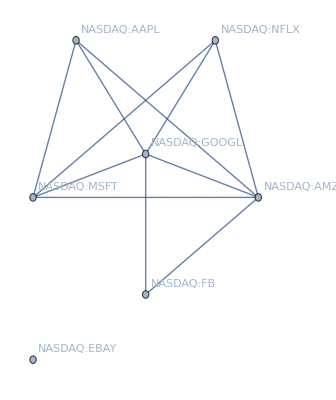

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:AMZN}

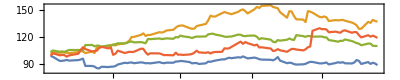

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX"}
r=FinancialData[#,"Return",{{2018},{2019}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58], GraphLayout->"RadialEmbedding", VertexLabels->"Name", ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[FinancialData[#,"CumulativeReturn",{{2012,1,1},{2012,5,25}}]&/@stocks,Joined-> True,AspectRatio-> 1/5, ImageSize->Full]
```

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX}

{{1.,0.638328,0.76617,0.634411,0.440314,0.737568,0.615193},{0.638328,1.,0.680435,0.450426,0.362342,0.639864,0.52214},{0.76617,0.680435,1.,0.529213,0.467707,0.758334,0.635409},{0.634411,0.450426,0.529213,1.,0.318276,0.584164,0.464231},{0.440314,0.362342,0.467707,0.318276,1.,0.387172,0.395068},{0.737568,0.639864,0.758334,0.584164,0.387172,1.,0.709716},{0.615193,0.52214,0.635409,0.464231,0.395068,0.709716,1.}}

-Graphics-

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:AMZN}

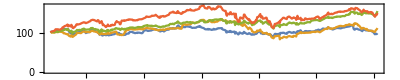

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX"}
r=FinancialData[#,"Return",{{2018},{2019}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58], GraphLayout->"RadialEmbedding", VertexLabels->"Name", ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[FinancialData[#,"CumulativeReturn",{{2018},{2019}}]&/@stocks,Joined-> True,AspectRatio-> 1/5, ImageSize->Full]
```

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{{1.,0.638328,0.76617,0.634411,0.440314,0.737568,0.615193,0.514946,0.422996},{0.638328,1.,0.680435,0.450426,0.362342,0.639864,0.52214,0.516637,0.419438},{0.76617,0.680435,1.,0.529213,0.467707,0.758334,0.635409,0.586236,0.421029},{0.634411,0.450426,0.529213,1.,0.318276,0.584164,0.464231,0.370161,0.31408},{0.440314,0.362342,0.467707,0.318276,1.,0.387172,0.395068,0.342146,0.2884},{0.737568,0.639864,0.758334,0.584164,0.387172,1.,0.709716,0.449993,0.485324},{0.615193,0.52214,0.635409,0.464231,0.395068,0.709716,1.,0.465024,0.428727},{0.514946,0.516637,0.586236,0.370161,0.342146,0.449993,0.465024,1.,0.333938},{0.422996,0.419438,0.421029,0.31408,0.2884,0.485324,0.428727,0.333938,1.}}

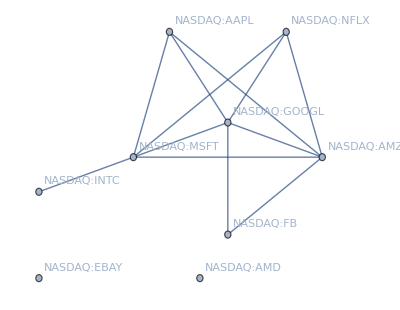

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:AMZN}

-Graphics-

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX", "NASDAQ:INTC", "NASDAQ:AMD"}
r=FinancialData[#,"Return",{{2018},{2019}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58], GraphLayout->"RadialEmbedding", VertexLabels->"Name", ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[FinancialData[#,"CumulativeReturn",{{2018},{2019}}]&/@stocks,Joined-> True,AspectRatio-> 1/5, ImageSize->Full]
```

```mathematica
CloudPut@(*Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX", "NASDAQ:INTC", "NASDAQ:AMD"}
r=FinancialData[#,"Return",{{2018},{2019}}]&/@dji
pos=Position[r,{}]
r=#["Values"]&/@Delete[r,pos]
dji = Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[.58], GraphLayout->"RadialEmbedding", VertexLabels->"Name", ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[FinancialData[#,"CumulativeReturn",{{2018},{2019}}]&/@stocks,Joined-> True,AspectRatio-> 1/5, ImageSize->Full]*)
```

```mathematica
Hold
```

```mathematica
CloudPut@
Hold@{
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks],
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX", "NASDAQ:INTC", "NASDAQ:AMD"},
r=FinancialData[#,"Return",{{2018},{2019}}]&/@dji,
pos=Position[r,{}],
r=#["Values"]&/@Delete[r,pos],
dji = Delete[dji,pos],
cor=Correlation[Transpose[r]],
portfolioMatrix[θ_]:= ReplacePart[cor,{i_,i_}-> 0]/.{x_/;x>θ->1,x_/;x<θ->0},
g=AdjacencyGraph[dji,portfolioMatrix[.58], GraphLayout->"RadialEmbedding", VertexLabels->"Name", ImageSize->Full],
stocks=First[FindClique[g]],
DateListPlot[FinancialData[#,"CumulativeReturn",{{2018},{2019}}]&/@stocks,Joined-> True,AspectRatio-> 1/5, ImageSize->Full]}
```

CloudObject[https://www.wolframcloud.com/objects/a1e52930-d923-42eb-8ce8-257245609a3c]